#### Problenm 10.4.28

```mathematica
fc[x_]:=Piecewise[{{0,-2<x<-1},{-x,-1<x<0},{x,0<x<1},{0,1<x<2}}]
```

```mathematica
fs[x_]:=Piecewise[{{0,-2<x<-1},{x,-1<x<0},{x,0<x<1},{0,1<x<2}}]
```

```mathematica
g[x_]:=(1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,m}]
```

```mathematica
g1[x_]:=(1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,10}]
```

```mathematica
g2[x_]:=(1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,20}]
```

```mathematica
g3[x_]:=(1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,30}]
```

```mathematica
g4[x_]:=(1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,50}]
```

```mathematica
h[x_]:=Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,m}]
```

```mathematica
h1[x_]:=Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,10}]
```

```mathematica
h2[x_]:=Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,20}]
```

```mathematica
h3[x_]:=Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,30}]
```

```mathematica
h4[x_]:=Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,50}]
```

#### Part c

Cosine Series

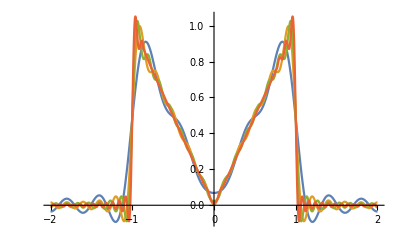

```mathematica
Plot[{g1[x],g2[x],g3[x],g4[x],feven[x]}, {x,-2,2}]
```

Sine Series

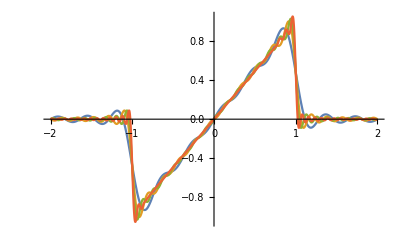

```mathematica
Plot[{h1[x],h2[x],h3[x],h4[x],fodd[x]},{x,-2,2}, PlotRange->Full]
```

```mathematica
((1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,m}])
```

### Part d

```mathematica
Manipulate[Plot[Abs[fc[x]-((1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*x/2], {n,m}])],{x,0,2},PlotRange-> {{0,2},{-1,1}}],{m,1,200}]
```

```mathematica
Manipulate[N[fc[1]-((1/4)+Sum[((2*Sin[n*Pi/2]/(n*Pi))+(4*Cos[n*Pi/2]/((n*Pi)^2))-(4/((n*Pi)^2)))*Cos[n*Pi*1/2], {n,m}])], {m,1,100}]
```

```mathematica
Manipulate[Plot[Abs[fs[x]-Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*x/2],{n,m}]],{x,0,2},PlotRange-> {{0,2},{-1,1}}],{m,1,200}]
```

```mathematica
Manipulate[N[fs[1]-Sum[((4*Sin[n*Pi/2]/((n*Pi)^2))-(2*Cos[n*Pi/2]/(n*Pi)))*Sin[n*Pi*1/2],{n,m}]], {m,1,100}]
```

### Problem 10.6.9

Part b

```mathematica
Int[x_]:=3*x+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Sin[n*Pi*x/20], {n,100}]
```

```mathematica
S[x_]:=3*x
```

```mathematica
Heat1x[x_]:=3*x+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*4]*Sin[n*Pi*x/20], {n,100}]
```

```mathematica
Heat2x[x_]:=3*x+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*20]*Sin[n*Pi*x/20], {n,100}]
```

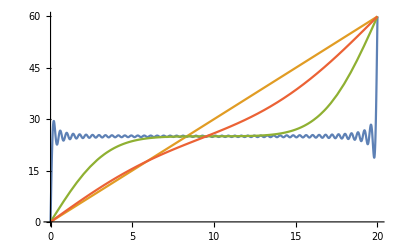

```mathematica
Plot[{Int[x],S[x],Heat1x[x],Heat2x[x]},{x,0,20}]
```

Part c

```mathematica
Heat1t[t_]:=3*5+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*t]*Sin[n*Pi*5/20], {n,100}]
```

```mathematica
Heat2t[t_]:=3*10+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*t]*Sin[n*Pi*10/20], {n,100}]
```

```mathematica
Heat3t[t_]:=3*15+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*t]*Sin[n*Pi*15/20], {n,100}]
```

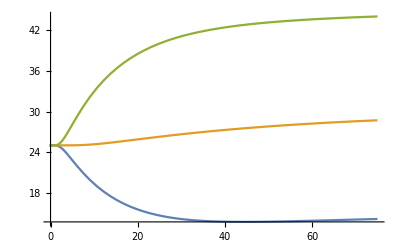

```mathematica
Plot[{Heat1t[t],Heat2t[t],Heat3t[t]}, {t,0,75}]
```

```mathematica
Plot3D[3*x+Sum[((70*Cos[n*Pi]+50)/(n*Pi))*Exp[(-1)*((n*Pi/20)^2)*0.86*t]*Sin[n*Pi*x/20], {n,100}], {x,0,20},{t,0,60},AxesLabel-> Automatic]
```

-Graphics3D-

#### Part d

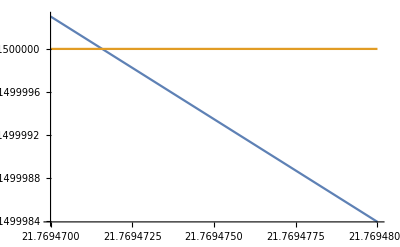

```mathematica
Plot[{Heat1t[t], 1.01*15}, {t,21.76947,21.76948}]
```

```mathematica
Heat1t[21.7694715799958]
```

15.15